```mathematica
Quit[];
```

```mathematica
(*healthy state*)
Wss=0;
Wgs=1.12;
Wsg=19;
Wgg=6.6;
Wcs=2.42;
Wxg=15.1;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS= 6 (*ms ??*);(*luam egal: tau_s=tau_g*);
(*scalam timpul -> delayul nou (in sistemul nostru) este Delta t / tauS *)
```

```mathematica
(*coeficientii pentru sistemul nostru*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*region spanned by alpha and beta, by varying Wgs and Wsg*)
p1=ParametricPlot[{alpha[Wgs,Wsg],beta[Wgs,Wsg]},{Wsg,0,30},{Wgs,0,20},PlotRange->All,PlotStyle->Red,Axes->False,Frame->True,PlotPoints->100]
```

-Graphics-

```mathematica
(*ecuatie curba *)
beta==(1-alpha/2)^2+(tau+1/tau)*(1-alpha/2)+1
```

beta==1+(1-alpha/2)^2+(1-alpha/2) (1/tau+tau)

```mathematica
(*intersection of all stability regions, for any tau>0*)
tau=.;
Reduce[ForAll[tau,tau>0,beta<(1-alpha/2)^2+(tau+1/tau)*(1-alpha/2)+1&&beta>alpha-1]]
```

alpha<2&&-1+alpha<beta<1/4 (16-8 alpha+alpha^2)

```mathematica
(*plot of S_1(alpha,beta)*)
plotIntersection=RegionPlot[beta<(1-alpha/2)^2+2*(1-alpha/2)+1&&beta>alpha-1,{alpha,-8,3},{beta,-10,20},Frame->True,Axes->False,AspectRatio->1,PlotPoints->300]
```

-Graphics-

```mathematica
Show[plotIntersection,p1,AspectRatio->1,PlotLabel->"Weak Gamma SD - healthy state parameters",LabelStyle->Directive[Bold,Black, FontSize->12],FrameLabel->{"α","β"}]
```

-Graphics-

```mathematica
Quit[];
```

```mathematica
(*DISEASED state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*luam egal: tau_s=tau_g*);
```

```mathematica
(*coefficients and function in rescaled system*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*critical value of tau deduced from Theorem 2.9*)
tau[Wgs_,Wsg_]:=If[((-4+alpha[Wgs,Wsg])^2-4 beta[Wgs,Wsg]) (alpha[Wgs,Wsg]^2-4 beta[Wgs,Wsg])>=0,Min[{(8+(-4+alpha[Wgs,Wsg]) alpha[Wgs,Wsg]+√(((-4+alpha[Wgs,Wsg])^2-4 beta[Wgs,Wsg]) (alpha[Wgs,Wsg]^2-4 beta[Wgs,Wsg]))-4 beta[Wgs,Wsg])/(4 (-2+alpha[Wgs,Wsg])),(8+(-4+alpha[Wgs,Wsg]) alpha[Wgs,Wsg]-√(((-4+alpha[Wgs,Wsg])^2-4 beta[Wgs,Wsg]) (alpha[Wgs,Wsg]^2-4 beta[Wgs,Wsg]))-4 beta[Wgs,Wsg])/(4 (-2+alpha[Wgs,Wsg]))}]]
```

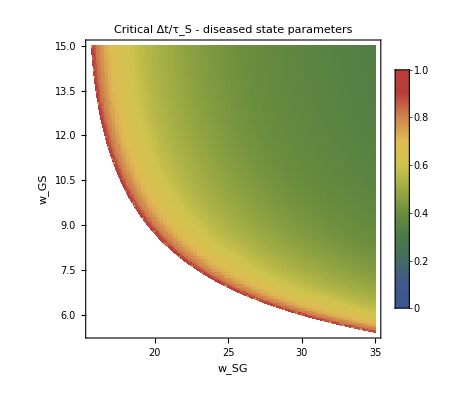

```mathematica
(*around diseased state parameters*)
DensityPlot[tau[Wgs,Wsg],{Wsg,10,35},{Wgs,5,15},PlotLegends->Automatic,PlotPoints->100,ColorFunction->"DarkRainbow",PlotRange->All,FrameLabel->{"w_SG","w_GS"},MeshFunctions->{#3&},Mesh->{{0.4,0.5,0.6,0.8}},PlotLabel->"Critical Δt/τ_S - diseased state parameters",LabelStyle->Directive[Bold,Black, FontSize->12]]
```